```mathematica
barJab = (1/Sqrt[2]){
{0,ⅈ Sqrt[2],-,0,0,-},{-ⅈ Sqrt[2],0,-,0,0,-},{,,0,0,0,ⅈ Sqrt[2]},
{0,0,0,0,ⅈ Sqrt[2],-},{0,0,0,-ⅈ Sqrt[2],0,-},{,,-ⅈ Sqrt[2],,,0}
};
bargab = {{0,-1,0,0,0,0},{-1,0,0,0,0,0},{0,0,1,0,0,1},{0,0,0,0,-1,0},{0,0,0,-1,0,0},{0,0,1,0,0,1}};
CommutationJabJcd[a_, b_, c_, d_]:= (
Print["[J",a,b,", J",c,d,"]=-i(g",b,d," J",a,c," - g",b,c," J",a,d," + g",a,c," J",b,d," - g",a,d," J",b,c,")"];
Print["[",barJab[[a, b]],",",barJab[[c, d]],"] = ", (-ⅈ)bargab[[b,d]]*barJab[[a,c]]," ",-(-ⅈ) bargab[[b,c]]*barJab[[a,d]]," ",+(-ⅈ) bargab[[a,c]]*barJab[[b,d]]," ",-(-ⅈ) bargab[[a,d]]*barJab[[b,c]]];
Print["[",barJab[[a, b]],",",barJab[[c, d]],"] = ", -ⅈ(bargab[[b,d]]*barJab[[a,c]]-bargab[[b,c]]*barJab[[a,d]]+ bargab[[a,c]]*barJab[[b,d]]- bargab[[a,d]]*barJab[[b,c]])];
)
barJab//MatrixForm
bargab//MatrixForm
CommutationJabJcd[3,1,2,3]
```

(0 | ⅈ ((l̂)_0)^+ | -((l̂)_1)^+/(√2) | 0 | 0 | -((l̂)_1)^-/(√2)
-ⅈ ((l̂)_0)^+ | 0 | -((l̂)_-1)^+/(√2) | 0 | 0 | -((l̂)_-1)^-/(√2)
((l̂)_1)^+/(√2) | ((l̂)_-1)^+/(√2) | 0 | 0 | 0 | ⅈ ((l̂)_0)^-
0 | 0 | 0 | 0 | ⅈ ((l̂)_0)^- | -((l̂)_1)^-/(√2)
0 | 0 | 0 | -ⅈ ((l̂)_0)^- | 0 | -((l̂)_-1)^-/(√2)
((l̂)_1)^-/(√2) | ((l̂)_-1)^-/(√2) | -ⅈ ((l̂)_0)^- | ((l̂)_1)^-/(√2) | ((l̂)_-1)^-/(√2) | 0)

(0 | -1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1)

[J31, J23]=-i(g13 J32 - g12 J33 + g32 J13 - g33 J12)

[((l̂)_1)^+/(√2),-((l̂)_-1)^+/(√2)] = 0 0 0 -((l̂)_0)^+

[((l̂)_1)^+/(√2),-((l̂)_-1)^+/(√2)] = -((l̂)_0)^+

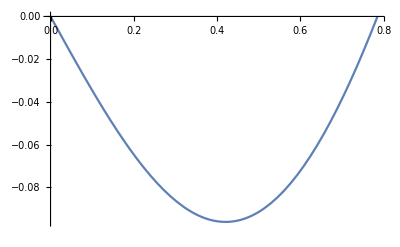

```mathematica
Plot[Sin[x](2Sin[x]Sin[x]-1)(1/(2Sqrt[2])),{x,0,Pi/4}]
```

```mathematica
fnsign[n_]:=Sign[n+(0.5)]
fnsign[{-1,0,1}]
```

{-1,1,1}

```mathematica
fsign[n_]:=Sign[-n-(0.5)]
signp05[n_]:=Sign[n+(0.5)]
INT22 = {{Cos[δ], Sin[δ]}, {Sin[δ], -Cos[δ]}};
LFDtoINFD = (1/Sqrt[2]){{1, 1}, {1, -1}};
nminus = {{1, 0}, {0, -Sign[n+(0.5)]}};
INT22//MatrixForm
LFDtoINFD//MatrixForm
nminus//MatrixForm
interpo = INT22.LFDtoINFD.nminus;
interpo//MatrixForm
FullSimplify[Inverse[interpo]]//MatrixForm
```

(Cos[δ] | Sin[δ]
Sin[δ] | -Cos[δ])

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

(1 | 0
0 | -Sign[0.5+n])

(Cos[δ]/(√2)+Sin[δ]/(√2) | -Sign[0.5+n] (Cos[δ]/(√2)-Sin[δ]/(√2))
-Cos[δ]/(√2)+Sin[δ]/(√2) | -Sign[0.5+n] (Cos[δ]/(√2)+Sin[δ]/(√2)))

((Cos[δ]+Sin[δ])/(√2) | (-Cos[δ]+Sin[δ])/(√2)
(-Cos[δ]+Sin[δ])/(√2 Sign[0.5+n]) | -(Cos[δ]+Sin[δ])/(√2 Sign[0.5+n]))

```mathematica
({{(Cos[δ]+Sin[δ])/(√2), (-Cos[δ]+Sin[δ])/(√2)}, {(-Cos[δ]+Sin[δ])/(√2 Sign[0.5+n]), -(Cos[δ]+Sin[δ])/(√2 Sign[0.5+n])}})
```

(1 | 0
0 | 1)

(1 | 0
0 | -Sign[0.5+n])

```mathematica
Simplify[LFDtoINFD.nminus]//MatrixForm
```

(1/(√2) | -Sign[0.5+n]/(√2)
1/(√2) | Sign[0.5+n]/(√2))

```mathematica
lp = (c+s) lhatp+(s-c) lhatm;
lm = ((s-c)/Sign[n+m+(0.5)]) lhatp-((c+s)/Sign[n+m+(0.5)]) lhatm;
expr=(c+s)(s-c) lp+Sign[n+(0.5)] Sign[m+(0.5)] (c+s)(c-s) lm;
Collect[expr,{lhatp,lhatm}]/.{s->1/2,c->1/2}
```

0

```mathematica
(c-s)^2*(-c+s)//FullSimplify
(-c+s)*(c+s)^2//FullSimplify
(c-s)^2*(c+s)//FullSimplify
```

-(c-s)^3

(-c+s) (c+s)^2

(c-s)^2 (c+s)

```mathematica
PDKbarJab = (1/Sqrt[2]){{0,-,-/Sqrt[2],0,0,0},{,0,/Sqrt[2],0,0,0},{/Sqrt[2],-/Sqrt[2],0,0,0,0},{0,0,0,0,-,-/Sqrt[2]},{0,0,0,,0,/Sqrt[2]},{0,0,0,/Sqrt[2],-/Sqrt[2],0}};
PKDkbarJab = (1/Sqrt[2]){{0,-(-)/Sqrt[2],-/Sqrt[2],0,0,0},{(-)/Sqrt[2],0,/Sqrt[2],0,0,0},{/Sqrt[2],-/Sqrt[2],0,0,0,0},{0,0,0,0,-(+)/Sqrt[2],-/Sqrt[2]},{0,0,0,(+)/Sqrt[2],0,/Sqrt[2]},{0,0,0,/Sqrt[2],-/Sqrt[2],0}};
Jab={{0,-,-/(√2),-/(√2),0,0},{,0,/(√2),/(√2),0,0},{/(√2),-/(√2),0,,0,0},{/(√2),-/(√2),-,0,0,0}, {0,0,0,0,0,0}, {0,0,0,0,0,0}};
PDKCommutationJabJcd[a_, b_, c_, d_]:= (
Print["[J",a,b,", J",c,d,"]=-i(g",b,d," J",a,c," - g",b,c," J",a,d," + g",a,c," J",b,d," - g",a,d," J",b,c,")"];
Print["[",PDKbarJab[[a, b]],",",PDKbarJab[[c, d]],"] = ", (-ⅈ)bargab[[b,d]]*PDKbarJab[[a,c]]," ",-(-ⅈ) bargab[[b,c]]*PDKbarJab[[a,d]]," ",+(-ⅈ) bargab[[a,c]]*PDKbarJab[[b,d]]," ",-(-ⅈ) bargab[[a,d]]*PDKbarJab[[b,c]]];
Print["[",PDKbarJab[[a, b]],",",PDKbarJab[[c, d]],"] = ", -ⅈ(bargab[[b,d]]*PDKbarJab[[a,c]]-bargab[[b,c]]*PDKbarJab[[a,d]]+ bargab[[a,c]]*PDKbarJab[[b,d]]- bargab[[a,d]]*PDKbarJab[[b,c]])];
)
PDKbarJab//MatrixForm
PDKCommutationJabJcd[3,1,2,3]
PKDkbarJab//MatrixForm
Jab//MatrixForm
Det[PDKbarJab]
Det[Jab]
charPolyM1=CharacteristicPolynomial[PDKbarJab,λ];
charPolyM2=CharacteristicPolynomial[Jab,λ];
```

(0 | -(D_-)/(√2) | -(k_-)/2 | 0 | 0 | 0
(D_-)/(√2) | 0 | (P_+)/2 | 0 | 0 | 0
(k_-)/2 | -(P_+)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(D_+)/(√2) | -(k_+)/2
0 | 0 | 0 | (D_+)/(√2) | 0 | (P_-)/2
0 | 0 | 0 | (k_+)/2 | -(P_-)/2 | 0)

[J31, J23]=-i(g13 J32 - g12 J33 + g32 J13 - g33 J12)

[(k_-)/2,(P_+)/2] = 0 0 0 -(ⅈ D_-)/(√2)

[(k_-)/2,(P_+)/2] = -(ⅈ D_-)/(√2)

(0 | 1/2 (-D+K^3) | -(k_-)/2 | 0 | 0 | 0
1/2 (D-K^3) | 0 | (P_+)/2 | 0 | 0 | 0
(k_-)/2 | -(P_+)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 (-D-K^3) | -(k_+)/2
0 | 0 | 0 | 1/2 (D+K^3) | 0 | (P_-)/2
0 | 0 | 0 | (k_+)/2 | -(P_-)/2 | 0)

(0 | -D | -(k_+)/(√2) | -(k_-)/(√2) | 0 | 0
D | 0 | (P_+)/(√2) | (P_-)/(√2) | 0 | 0
(k_+)/(√2) | -(P_+)/(√2) | 0 | K^3 | 0 | 0
(k_-)/(√2) | -(P_-)/(√2) | -K^3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

0

0

```mathematica
M1={{0,-(DD-K3)/2,-Kminus/2,0,0,0},{(DD-K3)/2,0,Pplus/2,0,0,0},{Kminus/2,-Pplus/2,0,0,0,0},{0,0,0,0,-(DD+K3)/2,-Kplus/2},{0,0,0,(DD+K3)/2,0,Pminus/2},{0,0,0,Kplus/2,-Pminus/2,0}};

(*Define the second matrix M2*)
M2={{0,-DD,-Kplus/Sqrt[2],-Kminus/Sqrt[2],0,0},{DD,0,Pplus/Sqrt[2],Pminus/Sqrt[2],0,0},{Kplus/Sqrt[2],-Pplus/Sqrt[2],0,K3,0,0},{Kminus/Sqrt[2],-Pminus/Sqrt[2],-K3,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}};
Print["M1 = ",M1//MatrixForm]
Print["M2 = ",M2//MatrixForm]
Print["{Rank[M1], Rank[M1]} = ",{MatrixRank[M1],MatrixRank[M2]}]
Print["{Determinant[M1], Determinant[M1]} = ",{Det[M1],Det[M2]}]
Print["{Trace[M1], Trace[M1]} = ",{Tr[M1],Tr[M2]}]
(*Print["{Eigenvalues[M1], Eigenvalues[M1]} = ",{Eigenvalues[M1]//FullSimplify,Eigenvalues[M2]//FullSimplify}]*)
charPolyM1=CharacteristicPolynomial[M1,λ];
charPolyM2=CharacteristicPolynomial[M2,λ];
Print["CharacteristicPolynomial of M1 - CharacteristicPolynomial of M2 = ",FullSimplify[charPolyM1-charPolyM2]]
Print["Eigenvalues[M1]-Eigenvalues[M2] = ",FullSimplify[Eigenvalues[M1]-Eigenvalues[M2]]]
```

M1 = (0 | 1/2 (-DD+K3) | -Kminus/2 | 0 | 0 | 0
(DD-K3)/2 | 0 | Pplus/2 | 0 | 0 | 0
Kminus/2 | -Pplus/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 (-DD-K3) | -Kplus/2
0 | 0 | 0 | (DD+K3)/2 | 0 | Pminus/2
0 | 0 | 0 | Kplus/2 | -Pminus/2 | 0)

M2 = (0 | -DD | -Kplus/(√2) | -Kminus/(√2) | 0 | 0
DD | 0 | Pplus/(√2) | Pminus/(√2) | 0 | 0
Kplus/(√2) | -Pplus/(√2) | 0 | K3 | 0 | 0
Kminus/(√2) | -Pminus/(√2) | -K3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

{Rank[M1], Rank[M1]} = {4,4}

{Determinant[M1], Determinant[M1]} = {0,0}

{Trace[M1], Trace[M1]} = {0,0}

CharacteristicPolynomial of M1 - CharacteristicPolynomial of M2 = 1/16 λ^2 (DD^4+K3^4+Kminus^2 Kplus^2+Kminus^2 Pminus^2-4 Kplus^2 Pminus^2+8 Kminus Kplus Pminus Pplus-4 Kminus^2 Pplus^2+Kplus^2 Pplus^2+Pminus^2 Pplus^2+2 DD K3 (Kminus^2-Kplus^2+8 Kplus Pminus-Pminus^2-8 Kminus Pplus+Pplus^2)-4 (Kminus^2+Kplus^2+Pminus^2+Pplus^2) λ^2+K3^2 (Kminus^2+Kplus^2+Pminus^2+Pplus^2-8 λ^2)+DD^2 (-18 K3^2+Kminus^2+Kplus^2+Pminus^2+Pplus^2-8 λ^2))

Eigenvalues[M1]-Eigenvalues[M2] = {0,0,1/2 (-√(-(DD+K3)^2-Kplus^2-Pminus^2)+√(-2 DD^2-2 K3^2-Kminus^2-Kplus^2-Pminus^2-Pplus^2-√(-4 (2 DD K3-Kplus Pminus+Kminus Pplus)^2+(2 DD^2+2 K3^2+Kminus^2+Kplus^2+Pminus^2+Pplus^2)^2))),1/2 (√(-(DD+K3)^2-Kplus^2-Pminus^2)-√(-2 DD^2-2 K3^2-Kminus^2-Kplus^2-Pminus^2-Pplus^2-√(-4 (2 DD K3-Kplus Pminus+Kminus Pplus)^2+(2 DD^2+2 K3^2+Kminus^2+Kplus^2+Pminus^2+Pplus^2)^2))),1/2 (-√(-(DD-K3)^2-Kminus^2-Pplus^2)+√(-2 DD^2-2 K3^2-Kminus^2-Kplus^2-Pminus^2-Pplus^2+√(-4 (2 DD K3-Kplus Pminus+Kminus Pplus)^2+(2 DD^2+2 K3^2+Kminus^2+Kplus^2+Pminus^2+Pplus^2)^2))),1/2 (√(-(DD-K3)^2-Kminus^2-Pplus^2)-√(-2 DD^2-2 K3^2-Kminus^2-Kplus^2-Pminus^2-Pplus^2+√(-4 (2 DD K3-Kplus Pminus+Kminus Pplus)^2+(2 DD^2+2 K3^2+Kminus^2+Kplus^2+Pminus^2+Pplus^2)^2)))}

```mathematica
gM1 = {{0,-1,0,0,0,0},{-1,0,0,0,0,0},{0,0,1,0,0,0},{0,0,0,0,-1,0},{0,0,0,-1,0,0},{0,0,0,0,0,1}};
gM2 = {{0,-1,0,0,0,0},{-1,0,0,0,0,0},{0,0,0,1,0,0},{0,0,1,0,0,0},{0,0,0,0,1,0}, {0,0,0,0,0,1}};
Print["gM1 = ",gM1 //MatrixForm]
Print["gM2 = ",gM2 //MatrixForm]
UM1=Transpose[Eigenvectors[gM1]];
M1D = Inverse[UM1].gM1.UM1;
Print["UM1= ",UM1// MatrixForm]
Print["gM1_{D} = UM1^{-1}.gM1.UM1= ",M1D// MatrixForm]
UM2=Transpose[Eigenvectors[gM2]];
M2D = Inverse[UM2].gM2.UM2;
Print["UM2= ",UM2// MatrixForm]
Print["gM2_{D} = UM2^{-1}.gM2.UM2= ",M2D// MatrixForm]
U=UM2.Inverse[UM1];
Print["U = UM2.Inverse[UM1] =", U//MatrixForm]
Print["M1 = U^{-1}.M2.U =  ",Inverse[U].M2.U//MatrixForm]
```

gM1 = (0 | -1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1)

gM2 = (0 | -1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

UM1= (0 | 1 | 0 | 0 | 0 | -1
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | -1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0)

gM1_{D} = UM1^{-1}.gM1.UM1= (-1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

UM2= (0 | 1 | 0 | 0 | 0 | -1
0 | 1 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0)

gM2_{D} = UM2^{-1}.gM2.UM2= (-1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

U = UM2.Inverse[UM1] =(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1/2 | -1/2 | 0
0 | 0 | 1 | 1/2 | 1/2 | 0
0 | 0 | 0 | -1/2 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 1)

M1 = U^{-1}.M2.U =  (0 | -DD | -Kminus/(√2)-Kplus/(√2) | -Kminus/(2 √2)+Kplus/(2 √2) | -Kminus/(2 √2)+Kplus/(2 √2) | 0
DD | 0 | Pminus/(√2)+Pplus/(√2) | Pminus/(2 √2)-Pplus/(2 √2) | Pminus/(2 √2)-Pplus/(2 √2) | 0
Kminus/(2 √2)+Kplus/(2 √2) | -Pminus/(2 √2)-Pplus/(2 √2) | 0 | K3/2 | K3/2 | 0
Kminus/(2 √2)-Kplus/(2 √2) | -Pminus/(2 √2)+Pplus/(2 √2) | -K3 | 0 | 0 | 0
Kminus/(2 √2)-Kplus/(2 √2) | -Pminus/(2 √2)+Pplus/(2 √2) | -K3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Define the commutator relations as functions*)(*Sign function for half-integer arguments*)
sgn[x_]:=Sign[x+1/2]

(*Commutator for l^+*)
CommLp[m_,n_,c_,s_]:=(m-n)*((FullSimplify[(c+s)^3-((c-s)^3*sgn[m]*sgn[n])/sgn[m+n]])*Lp[m+n]+(FullSimplify[(s-c) (c+s)^2-((c-s)^2 (c+s)*sgn[m]*sgn[n])/sgn[m+n]])*Lm[m+n])

(*Commutator for l^-*)
CommLm[m_,n_,c_,s_]:=(m-n)*((FullSimplify[(s-c)^3-((c+s)^3*sgn[m]*sgn[n])/sgn[m+n]])*Lm[m+n]+(FullSimplify[(s-c)^2 (c+s)+((s-c) (c+s)^2*sgn[m]*sgn[n])/sgn[m+n]])*Lp[m+n])

(*Commutator for mixed l^+and l^-*)
CommLpLm[m_,n_,c_,s_]:=(m-n)*((FullSimplify[(s-c) (c+s)^2-((c-s)^2 (c+s)*sgn[m]*sgn[n])/sgn[m+n]])*Lp[m+n]+(FullSimplify[(s-c)^2 (c+s)-((c-s) (c+s)^2*sgn[m]*sgn[n])/sgn[m+n]])*Lm[m+n])

(*Example Usage:Plug in values for m,n,c,s*)
mVal=-1;
nVal=0;
cVal=1/Sqrt[2];
sVal=0;

CommLp[mVal,nVal,cVal,sVal]
CommLm[mVal,nVal,cVal,sVal]
CommLpLm[mVal,nVal,cVal,sVal]
```

Lm[-1]/(√2)

Lm[-1]/(√2)

Lp[-1]/(√2)